```mathematica
Subscript[S, 1][{x_,y_}]:=-(x-1) (y-1) (-2+x+x^2+y+y^2)
Subscript[S, 2][{x_,y_}]:= -(x-1)^2 (x+1) (y-1)
Subscript[S, 3][{x_,y_}]:=(x-1)(x+1)^2(y-1)
Subscript[S, 4][{x_,y_}]:=(x+1)(y-1)(-2-x+x^2+y+y^2)
Subscript[S, 5][{x_,y_}]:= (x+1)(y-1)^2(y+1)
Subscript[S, 6][{x_,y_}]:=-(x+1)(y-1)(y+1)^2
Subscript[S, 7][{x_,y_}]:= -(x+1)(y+1)(-2-x+x^2-y+y^2)
Subscript[S, 8][{x_,y_}]:= -(x-1)(x+1)^2 (y+1)
Subscript[S, 9][{x_,y_}]:= (x-1)^2 (x+1) (y+1)
Subscript[S, 10][{x_,y_}]:=(x-1)(y+1)(-2+x+x^2-y+y^2)
Subscript[S, 11][{x_,y_}]:= (x-1)(y-1)(y+1)^2
Subscript[S, 12][{x_,y_}]:= -(x-1)(y-1)^2(y+1)

Subscript[n, 1]= {-1,-1}; 
Subscript[n, 2]={-1/3,-1};
Subscript[n, 3]= {1/3,-1};
Subscript[n, 4] = {1,-1};
Subscript[n, 5]={1,-1/3};
Subscript[n, 6]= {1,1/3};
Subscript[n, 7]={1,1};
Subscript[n, 8]={1/3,1};
Subscript[n, 9]={-1/3,1};
Subscript[n, 10] = {-1,1};
Subscript[n, 11] = {-1,1/3};
Subscript[n, 12]={-1,-1/3};
```

```mathematica
MatrixForm[Table[Subscript[S, i][{x,y}],{i,1,12}]]
MatrixForm[Expand[Table[Subscript[S, i][{x,y}],{i,1,12}]]]
```

((1-x) (-1+y) (-2+x+x^2+y+y^2)
-(-1+x)^2 (1+x) (-1+y)
(-1+x) (1+x)^2 (-1+y)
(1+x) (-1+y) (-2-x+x^2+y+y^2)
(1+x) (-1+y)^2 (1+y)
(-1-x) (-1+y) (1+y)^2
(-1-x) (1+y) (-2-x+x^2-y+y^2)
(1-x) (1+x)^2 (1+y)
(-1+x)^2 (1+x) (1+y)
(-1+x) (1+y) (-2+x+x^2-y+y^2)
(-1+x) (-1+y) (1+y)^2
(1-x) (-1+y)^2 (1+y))

(2-3 x+x^3-3 y+4 x y-x^3 y+y^3-x y^3
1-x-x^2+x^3-y+x y+x^2 y-x^3 y
1+x-x^2-x^3-y-x y+x^2 y+x^3 y
2+3 x-x^3-3 y-4 x y+x^3 y+y^3+x y^3
1+x-y-x y-y^2-x y^2+y^3+x y^3
1+x+y+x y-y^2-x y^2-y^3-x y^3
2+3 x-x^3+3 y+4 x y-x^3 y-y^3-x y^3
1+x-x^2-x^3+y+x y-x^2 y-x^3 y
1-x-x^2+x^3+y-x y-x^2 y+x^3 y
2-3 x+x^3+3 y-4 x y+x^3 y-y^3+x y^3
1-x+y-x y-y^2+x y^2-y^3+x y^3
1-x-y+x y-y^2+x y^2+y^3-x y^3)

```mathematica
MatrixForm[Table[Subscript[S, i][Subscript[n, j]]/8,{i,1,12},{j,1,12}]]
```

(1 | 20/27 | 7/27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/27 | 20/27
0 | 8/27 | 4/27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4/27 | 8/27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 7/27 | 20/27 | 1 | 20/27 | 7/27 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8/27 | 4/27 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4/27 | 8/27 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 7/27 | 20/27 | 1 | 20/27 | 7/27 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8/27 | 4/27 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/27 | 8/27 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/27 | 20/27 | 1 | 20/27 | 7/27
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8/27 | 4/27
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/27 | 8/27)

```mathematica
Table[Plot3D[Subscript[S, i][{x,y}]/8, {x,-1,1},{y,-1,1}],{i,1,12}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Subscript[G, i_][x_,y_]:=Grad[Subscript[S, i][{x,y}],{x,y}]
Subscript[G, i_,j_][x_,y_]:=(Subscript[G, i][x,y])[[j]]
```

```mathematica
MatrixForm[Table[Simplify[Subscript[G, i][x,y]],{i,1,12}]]
```

(-(-1+y) (-3+3 x^2+y+y^2) | -(-1+x) (-3+x+x^2+3 y^2)
-(-1-2 x+3 x^2) (-1+y) | -(-1+x)^2 (1+x)
(1+x) (-1+3 x) (-1+y) | (-1+x) (1+x)^2
(-1+y) (-3+3 x^2+y+y^2) | (1+x) (-3-x+x^2+3 y^2)
(-1+y)^2 (1+y) | (1+x) (-1+y) (1+3 y)
-(-1+y) (1+y)^2 | -(1+x) (-1+2 y+3 y^2)
-(1+y) (-3+3 x^2-y+y^2) | -(1+x) (-3-x+x^2+3 y^2)
-(-1+2 x+3 x^2) (1+y) | -(-1+x) (1+x)^2
(-1+x) (1+3 x) (1+y) | (-1+x)^2 (1+x)
(1+y) (-3+3 x^2-y+y^2) | (-1+x) (-3+x+x^2+3 y^2)
(-1+y) (1+y)^2 | (-1+x) (1+y) (-1+3 y)
-(-1+y)^2 (1+y) | -(-1+x) (-1-2 y+3 y^2))

```mathematica
Table[Plot3D[Subscript[G, i,1][x,y],{x,-1,1},{y,-1,1}],{i,1,12}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Subscript[G, 1,1][0,0]
Subscript[G, 4,1][1,-1]
```

2

8

```mathematica
Integrate[Subscript[S, 1][{x,y}]  Subscript[S, 5][{x,y}],{x,0,1},{y,0,1}]
```

2831/12600

```mathematica
Subscript[S, 1][ξ_,η_]:= 1/4(1-ξ)(1-η)
Subscript[S, 2][ξ_,η_]:= 1/4(1+ξ)(1-η)
Subscript[S, 3][ξ_,η_]:= 1/4(1+ξ)(1+η)
Subscript[S, 4][ξ_,η_]:= 1/4(1-ξ)(1+η)
```

```mathematica
P[ξ_,η_]:= x1 Subscript[S, 1][ξ,η]+x2 Subscript[S, 2][ξ,η]+x3 Subscript[S, 3][ξ,η]+x4 Subscript[S, 4][ξ,η]
Q[ξ_,η_]:= y1 Subscript[S, 1][ξ,η]+y2 Subscript[S, 2][ξ,η]+y3 Subscript[S, 3][ξ,η]+y4 Subscript[S, 4][ξ,η]
```

```mathematica
Simplify[x1 Subscript[S, 1][ξ,η] + x2 Subscript[S, 2][ξ,η] + x3 Subscript[S, 3][ξ,η] + x4 Subscript[S, 4][ξ,η]]
```

1/4 (x1 (-1+η) (-1+ξ)-x2 (-1+η) (1+ξ)+(1+η) (x3+x4+x3 ξ-x4 ξ))

```mathematica
Inverses=FullSimplify[Solve[x==P[ξ,η] && y==Q[ξ,η],{ξ,η,Reals}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ξ→-((x1 y-x2 y+x3 y-x4 y-x y1+x4 y1+x y2-x3 y2-x y3+x2 y3+x y4-x1 y4+√((x3 y-x4 y+x4 y1-x3 y2+x2 (-y+y3)+x1 (y-y4)+x (-y1+y2-y3+y4))^2+((x3-x4) (y1-y2)-(x1-x2) (y3-y4)) (-(x3+x4) (2 y-y1-y2)+x1 (2 y-y3-y4)+x2 (2 y-y3-y4)+2 x (-y1-y2+y3+y4))))/((x3-x4) (y1-y2)-(x1-x2) (y3-y4))),η→(-x1 y+x2 y-x3 y+x4 y+x y1-x2 y1-x y2+x1 y2+x y3-x4 y3-x y4+x3 y4+√((x3 y-x4 y+x4 y1-x3 y2+x2 (-y+y3)+x1 (y-y4)+x (-y1+y2-y3+y4))^2+((x3-x4) (y1-y2)-(x1-x2) (y3-y4)) (-(x3+x4) (2 y-y1-y2)+x1 (2 y-y3-y4)+x2 (2 y-y3-y4)+2 x (-y1-y2+y3+y4))))/((x1-x4) (y2-y3)-(x2-x3) (y1-y4))},{ξ→(-x1 y+x2 y-x3 y+x4 y+x y1-x4 y1-x y2+x3 y2+x y3-x2 y3-x y4+x1 y4+√((x3 y-x4 y+x4 y1-x3 y2+x2 (-y+y3)+x1 (y-y4)+x (-y1+y2-y3+y4))^2+((x3-x4) (y1-y2)-(x1-x2) (y3-y4)) (-(x3+x4) (2 y-y1-y2)+x1 (2 y-y3-y4)+x2 (2 y-y3-y4)+2 x (-y1-y2+y3+y4))))/((x3-x4) (y1-y2)-(x1-x2) (y3-y4)),η→-((x1 y-x2 y+x3 y-x4 y-x y1+x2 y1+x y2-x1 y2-x y3+x4 y3+x y4-x3 y4+√((x3 y-x4 y+x4 y1-x3 y2+x2 (-y+y3)+x1 (y-y4)+x (-y1+y2-y3+y4))^2+((x3-x4) (y1-y2)-(x1-x2) (y3-y4)) (-(x3+x4) (2 y-y1-y2)+x1 (2 y-y3-y4)+x2 (2 y-y3-y4)+2 x (-y1-y2+y3+y4))))/((x1-x4) (y2-y3)-(x2-x3) (y1-y4)))}}

```mathematica
R=ξ/.Inverses[[1,1]]
T=η /. Inverses[[1,2]]
```

-((y X⟦1⟧-y X⟦2⟧+y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ Y⟦3⟧+x Y⟦4⟧-X⟦1⟧ Y⟦4⟧+√((y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)))/(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)))

(-y X⟦1⟧+y X⟦2⟧-y X⟦3⟧+y X⟦4⟧+x Y⟦1⟧-X⟦2⟧ Y⟦1⟧-x Y⟦2⟧+X⟦1⟧ Y⟦2⟧+x Y⟦3⟧-X⟦4⟧ Y⟦3⟧-x Y⟦4⟧+X⟦3⟧ Y⟦4⟧+√((y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)))/((X⟦1⟧-X⟦4⟧) (Y⟦2⟧-Y⟦3⟧)+X⟦3⟧ (Y⟦1⟧-Y⟦4⟧)+X⟦2⟧ (-Y⟦1⟧+Y⟦4⟧))

```mathematica
Simplify[D[R,x]]
```

```mathematica
Subscript[J, 1,1] = Simplify[D[P[ξ,η],ξ]]
Subscript[J, 1,2] = Simplify[D[P[ξ,η],η]]
Subscript[J, 2,1] = Simplify[D[Q[ξ,η],ξ]]
Subscript[J, 2,2] = Simplify[D[Q[ξ,η],η]]
```

1/4 ((-1+η) x_1-(-1+η) x_2+(1+η) (x_3-x_4))

1/4 ((-1+ξ) x_1-(1+ξ) x_2+x_3+ξ x_3+x_4-ξ x_4)

1/4 ((-1+η) y_1-(-1+η) y_2+(1+η) (y_3-y_4))

1/4 ((-1+ξ) y_1-(1+ξ) y_2+y_3+ξ y_3+y_4-ξ y_4)

```mathematica
J={{1/4 ((-1+η) Subscript[x, 1]-(-1+η) Subscript[x, 2]+(1+η) (Subscript[x, 3]-Subscript[x, 4])),1/4 ((-1+η) Subscript[y, 1]-(-1+η) Subscript[y, 2]+(1+η) (Subscript[y, 3]-Subscript[y, 4]))},{1/4 ((-1+η) Subscript[y, 1]-(-1+η) Subscript[y, 2]+(1+η) (Subscript[y, 3]-Subscript[y, 4])),1/4 ((-1+ξ) Subscript[y, 1]-(1+ξ) Subscript[y, 2]+Subscript[y, 3]+ξ Subscript[y, 3]+Subscript[y, 4]-ξ Subscript[y, 4])}}
```

{{1/4 ((-1+η) x_1-(-1+η) x_2+(1+η) (x_3-x_4)),1/4 ((-1+η) y_1-(-1+η) y_2+(1+η) (y_3-y_4))},{1/4 ((-1+η) y_1-(-1+η) y_2+(1+η) (y_3-y_4)),1/4 ((-1+ξ) y_1-(1+ξ) y_2+y_3+ξ y_3+y_4-ξ y_4)}}

```mathematica
JI=Simplify[Inverse[J]]
```

```mathematica
prod1=Simplify[JI[[1,1]] Subscript[G, 2,1][P[ξ,η],Q[ξ,η]] Subscript[S, 3][{P[ξ,η],Q[ξ,η]}]]
```

```mathematica
integral=Integrate[prod1,{ξ,-1,1},{η,-1,1}]
```

```mathematica
Timing[Do[NIntegrate[testProd2,{ξ,-1,1},{η,-1,1},AccuracyGoal->10], 1000]]
```

{38.5,Null}

Test which solution is the appropriate one. It’s inv2.

```mathematica
inv1[x_,y_]:={-((y X⟦1⟧-y X⟦2⟧+y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ Y⟦3⟧+x Y⟦4⟧-X⟦1⟧ Y⟦4⟧+√((y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)))/(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧))),(-y X⟦1⟧+y X⟦2⟧-y X⟦3⟧+y X⟦4⟧+x Y⟦1⟧-X⟦2⟧ Y⟦1⟧-x Y⟦2⟧+X⟦1⟧ Y⟦2⟧+x Y⟦3⟧-X⟦4⟧ Y⟦3⟧-x Y⟦4⟧+X⟦3⟧ Y⟦4⟧+√((y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)))/((X⟦1⟧-X⟦4⟧) (Y⟦2⟧-Y⟦3⟧)+X⟦3⟧ (Y⟦1⟧-Y⟦4⟧)+X⟦2⟧ (-Y⟦1⟧+Y⟦4⟧))}

inv2[x_,y_]:={(-y X⟦1⟧+y X⟦2⟧-y X⟦3⟧+y X⟦4⟧+x Y⟦1⟧-X⟦4⟧ Y⟦1⟧-x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+x Y⟦3⟧-X⟦2⟧ Y⟦3⟧-x Y⟦4⟧+X⟦1⟧ Y⟦4⟧+√((y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)))/(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)), (y X⟦1⟧-y X⟦2⟧+y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦2⟧ Y⟦1⟧+x Y⟦2⟧-X⟦1⟧ Y⟦2⟧-x Y⟦3⟧+X⟦4⟧ Y⟦3⟧+x Y⟦4⟧-X⟦3⟧ Y⟦4⟧+√((y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)))/(-(X⟦1⟧-X⟦4⟧) (Y⟦2⟧-Y⟦3⟧)+X⟦2⟧ (Y⟦1⟧-Y⟦4⟧)+X⟦3⟧ (-Y⟦1⟧+Y⟦4⟧))}
```

```mathematica
X=.;Y=.;
```

```mathematica
(y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)
```

```mathematica
X={-10,-11,-12,-10};
Y={10,10,11,12};
inv1[-0.5,0.3]
inv2[0.5,0.3]
```

{-37.4832,-1.95842}

{1.17744,-22.2887}

```mathematica
Plot3D[inv1[x,y],{x,-10,-12},{y,10,12},PlotRange->{-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[inv2[x,y],{x,0,-2},{y,0,2}(*,PlotRange->{-1,1}*)]
```

-Graphics3D-

```mathematica
Module[{x,y},
{x=0.6; y=0.3;
P[x,y],
Q[x,y]}
]
```

{1.06,0.65}

Poenostavi izraz: Razvij do prvega ali drugega člena ter ga uporabi, kadar je imenovalec blizu 0, oz. kadar sta dve stranici vzporedni.

```mathematica
TeXForm[(-y X⟦1⟧+y X⟦2⟧-y X⟦3⟧+y X⟦4⟧+x Y⟦1⟧-X⟦4⟧ Y⟦1⟧-x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+x Y⟦3⟧-X⟦2⟧ Y⟦3⟧-x Y⟦4⟧+X⟦1⟧ Y⟦4⟧+√((y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)))/(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧))]
```

Part::partd: Part specification X⟦1⟧ is longer than depth of object.

Part::partd: Part specification X⟦2⟧ is longer than depth of object.

Part::partd: Part specification X⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

\frac{\sqrt{(-x Y[[1]]+x Y[[2]]-x Y[[3]]+x Y[[4]]+X[[2]] (Y[[3]]-y)+X[[1]]
   (y-Y[[4]])+y X[[3]]-y X[[4]]-X[[3]] Y[[2]]+X[[4]] Y[[1]])^2+(X[[3]]
   (Y[[1]]-Y[[2]])+X[[4]] (Y[[2]]-Y[[1]])-(X[[1]]-X[[2]]) (Y[[3]]-Y[[4]])) (-2 x
   Y[[1]]-2 x Y[[2]]+2 x Y[[3]]+2 x Y[[4]]+X[[1]] (2 y-Y[[3]]-Y[[4]])+X[[2]] (2
   y-Y[[3]]-Y[[4]])-2 y X[[3]]-2 y X[[4]]+X[[3]] Y[[1]]+X[[3]] Y[[2]]+X[[4]]
   Y[[1]]+X[[4]] Y[[2]])}+x Y[[1]]-x Y[[2]]+x Y[[3]]-x Y[[4]]-y X[[1]]+y X[[2]]-y
   X[[3]]+y X[[4]]+X[[1]] Y[[4]]-X[[4]] Y[[1]]+X[[3]] Y[[2]]-X[[2]] Y[[3]]}{X[[3]]
   (Y[[1]]-Y[[2]])+X[[4]] (Y[[2]]-Y[[1]])-(X[[1]]-X[[2]]) (Y[[3]]-Y[[4]])}

```mathematica
(*Pred korenom: *)
TeXForm[(-y X⟦1⟧+y X⟦2⟧-y X⟦3⟧+y X⟦4⟧+x Y⟦1⟧-X⟦4⟧ Y⟦1⟧-x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+x Y⟦3⟧-X⟦2⟧ Y⟦3⟧-x Y⟦4⟧+X⟦1⟧ Y⟦4⟧)/(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧))]
```

Part::partd: Part specification X⟦1⟧ is longer than depth of object.

Part::partd: Part specification X⟦2⟧ is longer than depth of object.

Part::partd: Part specification X⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
\frac{x y_1-x y_2+x y_3-x y_4-y x_1+y x_2-y x_3+y x_4+x_1
   y_4-x_4 y_1+x_3 y_2-x_2 y_3}{x_3 (y_1-y_2)+x_4
   (y_2-y_1)-(x_1-x_2) (y_3-y_4)}
```

```mathematica
TeXForm[y X⟦1⟧-y X⟦2⟧+y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦2⟧ Y⟦1⟧+x Y⟦2⟧-X⟦1⟧ Y⟦2⟧-x Y⟦3⟧+X⟦4⟧ Y⟦3⟧+x Y⟦4⟧-X⟦3⟧ Y⟦4⟧]
```

Part::partd: Part specification X⟦1⟧ is longer than depth of object.

Part::partd: Part specification X⟦2⟧ is longer than depth of object.

Part::partd: Part specification X⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
-x y_1+x y_2-x y_3+x y_4+y x_1-y x_2+y x_3-y x_4-x_1
   y_2+x_2 y_1+x_4 y_3-x_3 y_4
```

```mathematica
TeXForm[(y X⟦3⟧-y X⟦4⟧-x Y⟦1⟧+X⟦4⟧ Y⟦1⟧+x Y⟦2⟧-X⟦3⟧ Y⟦2⟧-x Y⟦3⟧+X⟦2⟧ (-y+Y⟦3⟧)+X⟦1⟧ (y-Y⟦4⟧)+x Y⟦4⟧)^2+(X⟦3⟧ (Y⟦1⟧-Y⟦2⟧)+X⟦4⟧ (-Y⟦1⟧+Y⟦2⟧)-(X⟦1⟧-X⟦2⟧) (Y⟦3⟧-Y⟦4⟧)) (-2 y X⟦3⟧-2 y X⟦4⟧-2 x Y⟦1⟧+X⟦3⟧ Y⟦1⟧+X⟦4⟧ Y⟦1⟧-2 x Y⟦2⟧+X⟦3⟧ Y⟦2⟧+X⟦4⟧ Y⟦2⟧+2 x Y⟦3⟧+X⟦1⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+X⟦2⟧ (2 y-Y⟦3⟧-Y⟦4⟧)+2 x Y⟦4⟧)]
```

Part::partd: Part specification X⟦3⟧ is longer than depth of object.

Part::partd: Part specification X⟦4⟧ is longer than depth of object.

Part::partd: Part specification Y⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(-x y_1+x y_2-x y_3+x y_4+x_2 (y_3-y)+x_1 (y-y_4)+y x_3-y
   x_4-x_3 y_2+x_4 y_1)^2+(x_3 (y_1-y_2)+x_4
   (y_2-y_1)-(x_1-x_2) (y_3-y_4)) (-2 x y_1-2 x y_2+2 x
   y_3+2 x y_4+x_1 (2 y-y_3-y_4)+x_2 (2 y-y_3-y_4)-2 y
   x_3-2 y x_4+x_3 y_1+x_3 y_2+x_4 y_1+x_4 y_2)
```

```mathematica
vars={1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,
	x y, x^2 y,x^3 y,x^4 y,x^5 y,x^6 y,x^7 y,x^8 y,x^9 y,x^10 y,x^11 y,x^12 y,
	x y^2, x^2 y^2,x^3 y^2,x^4 y^2,x^5 y^2,x^6 y^2,x^7 y^2,x^8 y^2,x^9 y^2,x^10 y^2,x^11 y^2,x^12 y^2,
	x y^3, x^2 y^3,x^3 y^3,x^4 y^3,x^5 y^3,x^6 y^3,x^7 y^3,x^8 y^3,x^9 y^3,x^10 y^3,x^11 y^3,x^12 y^3,}
```

```mathematica
vars = Table[x^i y^j, {i,0,12},{j,0,12}];
vars//TableForm
```

1 | y | y^2 | y^3 | y^4 | y^5 | y^6 | y^7 | y^8 | y^9 | y^10 | y^11 | y^12
x | x y | x y^2 | x y^3 | x y^4 | x y^5 | x y^6 | x y^7 | x y^8 | x y^9 | x y^10 | x y^11 | x y^12
x^2 | x^2 y | x^2 y^2 | x^2 y^3 | x^2 y^4 | x^2 y^5 | x^2 y^6 | x^2 y^7 | x^2 y^8 | x^2 y^9 | x^2 y^10 | x^2 y^11 | x^2 y^12
x^3 | x^3 y | x^3 y^2 | x^3 y^3 | x^3 y^4 | x^3 y^5 | x^3 y^6 | x^3 y^7 | x^3 y^8 | x^3 y^9 | x^3 y^10 | x^3 y^11 | x^3 y^12
x^4 | x^4 y | x^4 y^2 | x^4 y^3 | x^4 y^4 | x^4 y^5 | x^4 y^6 | x^4 y^7 | x^4 y^8 | x^4 y^9 | x^4 y^10 | x^4 y^11 | x^4 y^12
x^5 | x^5 y | x^5 y^2 | x^5 y^3 | x^5 y^4 | x^5 y^5 | x^5 y^6 | x^5 y^7 | x^5 y^8 | x^5 y^9 | x^5 y^10 | x^5 y^11 | x^5 y^12
x^6 | x^6 y | x^6 y^2 | x^6 y^3 | x^6 y^4 | x^6 y^5 | x^6 y^6 | x^6 y^7 | x^6 y^8 | x^6 y^9 | x^6 y^10 | x^6 y^11 | x^6 y^12
x^7 | x^7 y | x^7 y^2 | x^7 y^3 | x^7 y^4 | x^7 y^5 | x^7 y^6 | x^7 y^7 | x^7 y^8 | x^7 y^9 | x^7 y^10 | x^7 y^11 | x^7 y^12
x^8 | x^8 y | x^8 y^2 | x^8 y^3 | x^8 y^4 | x^8 y^5 | x^8 y^6 | x^8 y^7 | x^8 y^8 | x^8 y^9 | x^8 y^10 | x^8 y^11 | x^8 y^12
x^9 | x^9 y | x^9 y^2 | x^9 y^3 | x^9 y^4 | x^9 y^5 | x^9 y^6 | x^9 y^7 | x^9 y^8 | x^9 y^9 | x^9 y^10 | x^9 y^11 | x^9 y^12
x^10 | x^10 y | x^10 y^2 | x^10 y^3 | x^10 y^4 | x^10 y^5 | x^10 y^6 | x^10 y^7 | x^10 y^8 | x^10 y^9 | x^10 y^10 | x^10 y^11 | x^10 y^12
x^11 | x^11 y | x^11 y^2 | x^11 y^3 | x^11 y^4 | x^11 y^5 | x^11 y^6 | x^11 y^7 | x^11 y^8 | x^11 y^9 | x^11 y^10 | x^11 y^11 | x^11 y^12
x^12 | x^12 y | x^12 y^2 | x^12 y^3 | x^12 y^4 | x^12 y^5 | x^12 y^6 | x^12 y^7 | x^12 y^8 | x^12 y^9 | x^12 y^10 | x^12 y^11 | x^12 y^12

```mathematica
Length[vars]
```

13

```mathematica
169
```

```mathematica
Integrate[x^2,{x,-1,1},{y,-1,1}]
```

4/3

```mathematica
polys=Table[LegendreP[i,x],{i,0,7}];
polys//TableForm
```

1
x
1/2 (-1+3 x^2)
1/2 (-3 x+5 x^3)
1/8 (3-30 x^2+35 x^4)
1/8 (15 x-70 x^3+63 x^5)
1/16 (-5+105 x^2-315 x^4+231 x^6)
1/16 (-35 x+315 x^3-693 x^5+429 x^7)

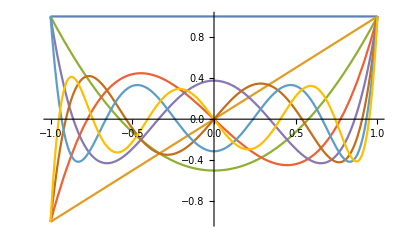

```mathematica
Plot[polys,{x,-1,1}]
```